## “HUT” Function:

```mathematica
Clear[Q,ω0,ω1,ω2,n,ncolumnas,norder];
```

```mathematica
Definitions:
```

```mathematica
Q[1,x_]:=-2 x^2;
ω0[x_]:=2 x^2(2 x^2-6 x+1);
ω1[x_]:=2 x^2(-4 x^2+8 x-1);
ω2[x_]:=4 x^3(x-1);
```

```mathematica
Recurrence:
```

```mathematica
n=350;
nfilas=n;
ncolumnas=2;
Polinomios=Table[0,nfilas,ncolumnas];
For[i=1,i≤nfilas,i++,Polinomios[[i,1]]=i;];
Polinomios[[1,2]]=Q[1,x];
For[norder=1,norder<n,norder+=1,
Q[norder+1,x]=Simplify[Q[norder,x]ω0[x]+D[Q[norder,x],x]ω1[x]+D[Q[norder,x],x,x]ω2[x]];
Polinomios[[norder+1,2]]=Q[norder+1,x];
];
```

```mathematica
Hut Function :
```

```mathematica
SET[y_]:=Table[{n1,Simplify[Abs[Polinomios[[n1,2]]/.x->y]/(n1!)]},{n1,1,n}]
```

#### Plot |Q_l(x)/l!| vs l:

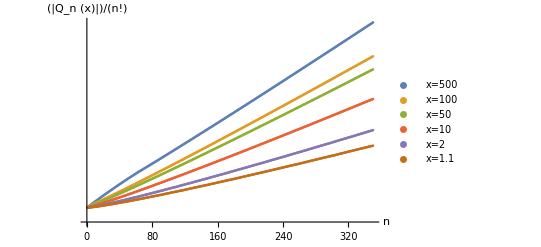

```mathematica
ListLogPlot[{SET[500],SET[100],SET[50],SET[10],SET[2],SET[SetPrecision[1.1,10000]]},AxesLabel->{"n","(|Q_n (x)|)/(n!)"},PlotLegends->{"x=500","x=100","x=50","x=10","x=2", "x=1.1"}]
```

```mathematica
SETDIFF[y_]:=Table[{n1,Simplify[Log[Abs[Polinomios[[n1+1,2]]/.x->y]/((n1+1)!)]-Log[Abs[Polinomios[[n1,2]]/.x->y]/(n1!)]]},{n1,1,n-1}]
```

#### Plot Log[|Q_(l+1)|/(l+1)!] - Log[|Q_l|/l!] vs l:

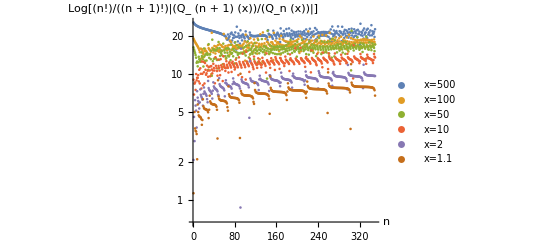

```mathematica
ListLogPlot[{SETDIFF[500],SETDIFF[100],SETDIFF[50],SETDIFF[10],SETDIFF[2],SETDIFF[SetPrecision[1.1,10000]]},AxesLabel->{"n","Log[(n!)/((n + 1)!)|(Q_ (n + 1) (x))/(Q_n (x))|]"},PlotLegends->{"x=500","x=100","x=50","x=10","x=2","x=1.1"}]
```

```mathematica
Q[y_,l_]:=Polinomios[[l,2]]/.x->y;
Coefficients[y_,l_]:=Table[{n1,Abs[Coefficient[Q[y,l],y,n1]]},{n1,0,Exponent[Q[y,l],y]}];
```

#### Plot Coefficient |Q_l(x)| vs Degree:

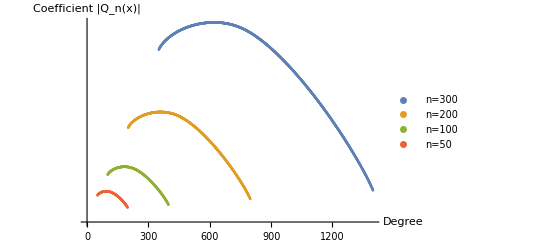

```mathematica
ListLogPlot[{Coefficients[y,350],Coefficients[y,200],Coefficients[y,100],Coefficients[y,50]},AxesLabel->{"Degree","Coefficient |Q_n(x)|"},PlotLegends->{"n=300","n=200","n=100","n=50"}]
```

#### Table of Coefficients:

```mathematica
Coeff[l_,n_]:=Abs[Coefficient[Q[y,l],y,n]];
CoeffTable:=Table[N[Coeff[l,n1]],{l,1,n},{n1,0,Exponent[Q[y,l],y]}];
```

```mathematica
filas=Table["l="<>ToString[i],{i,1,n}];
columnas=Table["n="<>ToString[i],{i,0,Exponent[Q[y,n],y]}];
Grid[{{Style["Table of coefficients C(l,n)",Bold,16],SpanFromAbove},{TableForm[CoeffTable, TableHeadings->{filas,columnas}]}}, Alignment->Left]
```

Table of coefficients C(l,n) | 
 | n=0 | n=1 | n=2 | n=3 | n=4 | n=5 | n=6 | n=7 | n=8 | n=9 | n=10 | n=11 | n=12 | n=13 | n=14 | n=15 | n=16 | n=17 | n=18 | n=19 | n=20 | n=21 | n=22 | n=23 | n=24 | n=25 | n=26 | n=27 | n=28 | n=29 | n=30 | n=31 | n=32 | n=33 | n=34 | n=35 | n=36 | n=37 | n=38
l=1 | 0. | 0. | 2. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
l=2 | 0. | 0. | 0. | 24. | 84. | 56. | 8. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
l=3 | 0. | 0. | 0. | 0. | 720. | 6480. | 15480. | 13920. | 4992. | 704. | 32. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
l=4 | 0. | 0. | 0. | 0. | 0. | 40320. | 665280. | 3.1248×10^6 | 6.24792×10^6 | 6.07824×10^6 | 2.99107×10^6 | 752768. | 95808. | 5760. | 128. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
l=5 | 0. | 0. | 0. | 0. | 0. | 0. | 3.6288×10^6 | 9.43488×10^7 | 7.15841×10^8 | 2.42077×10^9 | 4.28685×10^9 | 4.2619×10^9 | 2.44468×10^9 | 8.17588×10^8 | 1.60158×10^8 | 1.82589×10^7 | 1.1735×10^6 | 38912. | 512. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
l=6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.79002×10^8 | 1.79626×10^10 | 1.98626×10^11 | 1.00059×10^12 | 2.7344×10^12 | 4.41295×10^12 | 4.3874×10^12 | 2.73983×10^12 | 1.08402×10^12 | 2.73295×10^11 | 4.40503×10^10 | 4.5238×10^9 | 2.9097×10^8 | 1.12282×10^7 | 235520. | 2048. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
l=7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.71783×10^10 | 4.44609×10^12 | 6.71709×10^13 | 4.67797×10^14 | 1.80236×10^15 | 4.21865×10^15 | 6.3154×10^15 | 6.21794×10^15 | 4.08349×10^15 | 1.80131×10^15 | 5.36348×10^14 | 1.08294×10^14 | 1.48708×10^13 | 1.38651×10^12 | 8.69021×10^10 | 3.57428×10^9 | 9.18159×10^7 | 1.3271×10^6 | 8192. |  |  |  |  |  |  |  |  |  |  |  | 
l=8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.09228×10^13 | 1.39137×10^15 | 2.74612×10^16 | 2.51559×10^17 | 1.2902×10^18 | 4.09048×10^18 | 8.48932×10^18 | 1.19311×10^19 | 1.15786×10^19 | 7.84079×10^18 | 3.72574×10^18 | 1.24722×10^18 | 2.95358×10^17 | 4.96851×10^16 | 5.95335×10^15 | 5.07813×10^14 | 3.06476×10^13 | 1.28959×10^12 | 3.67678×10^10 | 6.73333×10^8 | 7.11066×10^6 | 32768. |  |  |  |  |  |  |  | 
l=9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.40237×10^15 | 5.37799×10^17 | 1.34151×10^19 | 1.5596×10^20 | 1.02301×10^21 | 4.1957×10^21 | 1.14387×10^22 | 2.15334×10^22 | 2.86602×10^22 | 2.73538×10^22 | 1.88707×10^22 | 9.45203×10^21 | 3.44837×10^21 | 9.19462×10^20 | 1.79883×10^20 | 2.59202×10^19 | 2.75795×10^18 | 2.16702×10^17 | 1.25257×10^16 | 5.27575×10^14 | 1.59041×10^13 | 3.32503×10^11 | 4.55816×10^9 | 3.67002×10^7 | 131072. |  |  |  | 
l=10 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.4329×10^18 | 2.51805×10^20 | 7.73809×10^21 | 1.11113×10^23 | 9.04914×10^23 | 4.64436×10^24 | 1.60144×10^25 | 3.86508×10^25 | 6.70586×10^25 | 8.50836×10^25 | 7.97856×10^25 | 5.56369×10^25 | 2.89537×10^25 | 1.12734×10^25 | 3.29311×10^24 | 7.2413×10^23 | 1.20316×10^23 | 1.51583×10^22 | 1.45156×10^21 | 1.05698×10^20 | 5.8386×10^18 | 2.43101×10^17 | 7.53901×10^15 | 1.70654×10^14 | 2.72667×10^12 | 2.90217×10^10 | 1.84025×10^8 | 524288. |

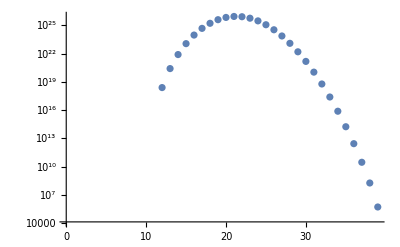

```mathematica
ListLogPlot[CoeffTable[[n]]]
```